# Homework 7

## Wang Long 1101110160

Mathematica 8.0

## 1. ΛCDM model, estimate the age of universe and the size of particle horizon.

```mathematica
h0=0.72;
ΩΛ0=0.75;
Ωm0=0.25;
Ωr0=0;
Ωk0=0;
H0=h0*100 km s^-1 Mpc^-1;
c=3*^5km/s;
a0=1;
```

### The age of the Universe

```mathematica
Subscript[t, 0]= 1/H0∫_0^1 1/(x √(ΩΛ0+Ωm0 x^-3+Ωr0 x^-4+Ωk0 x^-2))ⅆx (Gyr)/.{Mpc->3.08567756*^19 km,s->1/(1*^9*365*24*3600)}
```

13.7772 Gyr

### The size of particle horizon

```mathematica
Subscript[d, p]=c/H0∫_0^1 1/(x^2 √(ΩΛ0+Ωm0 x^-3+Ωr0 x^-4+Ωk0 x^-2))ⅆx /.{ km->1/3.08567756*^19Mpc,s->1/(1*^9*365*24*3600)}
```

14824.7 Mpc

## 2. Estimate the proper and comoving size of the particle horizon, also estimate the enclosed mass

```mathematica
at[T_]:=2.585*^-4eV/T;
dp[a_]:=c/H0 NIntegrate[1/(x^2 √(ΩΛ0+Ωm0 x^-3+Ωr0 x^-4+Ωk0 x^-2)),{x,0,a}](Mpc^-1)/.{ km->1/3.08567756*^19Mpc,s->1/(1*^9*365*24*3600)}
ρc0=2.776*^11 h0^2(*Subscript[M, sun] Mpc^-3*) ;
ρm0=Ωm0*ρc0;
Tlist={1*^24,1*^11,1*^8,1*^6}*eV;
alist={3*^-4,1/(1+1*^3),1/(1+20)}//N;
Grid[{
{"","GUT","EW","QCD","BBN","MRE","REC","FFS"},
{"T","10^15GeV","100GeV","100MeV","1MeV","",""},
Flatten@{"a",at/@Tlist,alist},
Flatten@{"d_(P, comv)(Mpc)",dp[at[#]]&/@Tlist,dp/@alist},
Flatten@{"d_(p, prop)(Mpc)",at[#]*dp[at[#]]&/@Tlist,#*dp[#]&/@alist},
Flatten@{"ρ_M(M_sunMpc^-3)",ρm0*at[#]^-3&/@Tlist,ρm0*#^-3&/@alist},
Flatten@{"M_eclosed(M_sun)",ρm0*(dp[at[#]])^3&/@Tlist,ρm0*(dp[#])^3&/@alist}
},Frame->All]
"EW:electroweak scale, MRE:matter-radiation equalit, REC:recombination, FFS:formation of first stars";
```

| GUT | EW | QCD | BBN | MRE | REC | FFS
T | 10^15GeV | 100GeV | 100MeV | 1MeV |  |  | 
a | 2.585×10^-28 | 2.585×10^-15 | 2.585×10^-12 | 2.585×10^-10 | 0.0003 | 0.000999001 | 0.047619
d_(P, comv)(Mpc) | 2.67966×10^-10 | 0.000847382 | 0.0267966 | 0.267966 | 288.675 | 526.783 | 3636.88
d_(p, prop)(Mpc) | 6.92691×10^-38 | 2.19048×10^-18 | 6.92691×10^-14 | 6.92691×10^-11 | 0.0866025 | 0.526257 | 173.185
ρ_M(M_sunMpc^-3) | 2.08278×10^93 | 2.08278×10^54 | 2.08278×10^45 | 2.08278×10^39 | 1.33248×10^21 | 3.6085×10^19 | 3.33183×10^14
M_eclosed(M_sun) | 6.92248×10^-19 | 21.8908 | 692248. | 6.92248×10^8 | 8.65471×10^17 | 5.2592×10^18 | 1.73066×10^21

## 3. Draw the Penrose diagram

### A flat de Sitter space

ds^2=-dt^2+a^2(dr^2+r^2 dΩ^2)
a=(6π G ρ_0)^(1/3)t^(2/3)=a_0 t^(2/3)
→ ds^2=a^2(-(3 a_0^-1 dt^(1/3))^2+dr^2+r^2 dΩ^2)

```mathematica
tds[a0_,η_,χ_]:=1/2(Tan[(3 a0^-1 η^(1/3)+χ)/2]+Tan[(3 a0^-1 η^(1/3)-χ)/2]);
rds[a0_,η_,χ_]:=1/2(Tan[(3 a0^-1 η^(1/3)+χ)/2]-Tan[(3 a0^-1 η^(1/3)-χ)/2]);
ds2ds=Simplify[-(D[tds[Subscript[a, 0],η,χ],η]*dη+D[tds[Subscript[a, 0],η,χ],χ]*dχ)^2+(D[rds[Subscript[a, 0],η,χ],η]*dη+D[rds[Subscript[a, 0],η,χ],χ]*dχ)^2]
```

(Sec[1/2 (-χ+(3 η^(1/3))/a_0)]^2 Sec[1/2 (χ+(3 η^(1/3))/a_0)]^2 (-dη^2+dχ^2 η^(4/3) a_0^2))/(4 η^(4/3) a_0^2)

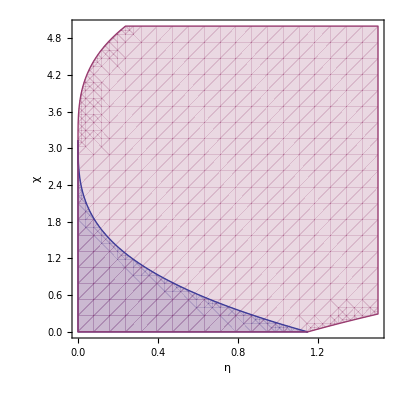

```mathematica
RegionPlot[{-π<3 η^(1/3)+χ<π,-π<3 η^(1/3)-χ<π},{η,0,1.5},{χ,0,5},FrameLabel->{η,χ}]
```

### A flat radiation dominated universe

ds^2=-dt^2+a^2(dr^2+r^2 dΩ^2)
a=(32π G ρ_0/3)^(1/2)t^(1/2)=a_0 t^(1/2)
→ ds^2=a^2(-(2 a_0^-1 dt^(1/2))^2+dr^2+r^2 dΩ^2)

```mathematica
trd[a0_,η_,χ_]:=1/2(Tan[(2 a0^-1 η^(1/2)+χ)/2]+Tan[(2 a0^-1 η^(1/2)-χ)/2]);
rrd[a0_,η_,χ_]:=1/2(Tan[(2 a0^-1 η^(1/2)+χ)/2]-Tan[(2 a0^-1 η^(1/2)-χ)/2]);
ds2rd=Simplify[-(D[trd[Subscript[a, 0],η,χ],η]*dη+D[trd[Subscript[a, 0],η,χ],χ]*dχ)^2+(D[rrd[Subscript[a, 0],η,χ],η]*dη+D[rrd[Subscript[a, 0],η,χ],χ]*dχ)^2]
```

(Sec[χ/2-(√η)/a_0]^2 Sec[χ/2+(√η)/a_0]^2 (-dη^2+dχ^2 η a_0^2))/(4 η a_0^2)

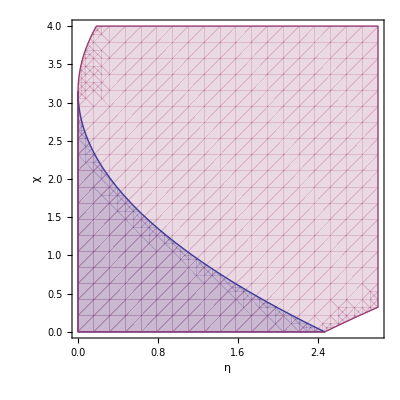

```mathematica
RegionPlot[{-π<2 η^(1/2)+χ<π,-π<2 η^(1/2)-χ<π},{η,0,3},{χ,0,4},FrameLabel->{η,χ}]
```